## Miscellaneous

### pyramids temp

```mathematica
conv2[A_?NumericQ,B_]:=conv2[{{A}},B];
conv2[A_?VectorQ,B_]:=conv2[{A},B];
conv2[A_,B_]:=ListConvolve[A,B,{1,-1},0];
```

```mathematica
ClearAll[makePyramidC];
makePyramidC[image_,level_Integer,blurRadius_]:=Module[{filter,F,imdata,ny,nx,ind0x,ind0y,ind1x,ind1y,
ind2x,ind2y,simg,pyramid,pyramidgradX,pyramidgradY,gradX,gradY},
pyramid=pyramidgradX=pyramidgradY={};
If[blurRadius>0,
filter=1;
F=conv2[{1,2,1},List/@{1,2,1}]/16.;
filter=Nest[conv2[#,F]&,filter,blurRadius]
];
Do[
If[i==1,
imdata=ImageData[image],
imdata=pyramid[[i-1]];
{ny,nx}=Dimensions[imdata];

{ind0x,ind0y } = Range[1,#,2]&/@{nx-1,ny-1};
{ind1x,ind1y} = Range[2,#,2]&/@{nx,ny};
{ind2x,ind2y} = Range[3,#,2]&/@{nx,ny};

If[Length[ind2x]<Length[ind1x],AppendTo[ind2x,Last@ind2x]];
If[Length[ind2y]<Length[ind1y],AppendTo[ind2y,Last@ind2y]];

simg=0.125*imdata[[ind1y,ind1x]];
simg=Fold[#1+0.125imdata[[#2[[1]],#2[[2]]]]&,simg,{{ind1y,ind0x},{ind0y,ind1x},{ind1y,ind2x},
{ind2y,ind1x}}];
imdata=Fold[#1+0.0625imdata[[#2[[1]],#2[[2]]]]&,simg,{{ind0y,ind0x},{ind0y,ind2x},{ind2y,ind2x},
{ind2y,ind0x}}];
];
If[filter≠ {},
imdata=conv2[filter,imdata][[2;;-2,2;;-2]]
];
gradX = conv2[{{1,0,-1}},imdata][[All,2;;-2]];
gradY=Thread[conv2[{{1,0,-1}},Transpose@imdata]][[2;;-2]];
AppendTo[pyramid,imdata];
AppendTo[pyramidgradX,gradX];
AppendTo[pyramidgradY,gradY],{i,level}];
{pyramid,pyramidgradX,pyramidgradY}
];
```

```mathematica
{pyramid,pyramidgradX,pyramidgradY}=makePyramidC[-Graphics-,2,1];
```

```mathematica
Map[ImageAdjust@*Image,Join[pyramid,pyramidgradX,pyramidgradY]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Pyramids Builtin

```mathematica
ClearAll[makePyramidBuiltin,fx,fy,makePyramidFunc];
SetAttributes[makePyramidBuiltin,HoldAll];
SetAttributes[makePyramidBuiltin,HoldAll];
makePyramidFunc[key:1|2]:=Switch[key,1,
SetDelayed@@Hold[fx,ImageConvolve[#,{{-1,0,1},{-1,0,1},{-1,0,1}}]&];
SetDelayed@@Hold[fy,ImageConvolve[#,{{1,1,1},{0,0,0},{-1,-1,-1}}]&],
2,
SetDelayed@@Hold[fx,GaussianFilter[#,1,{0,1}]&];
SetDelayed@@Hold[fy,GaussianFilter[#,1,{1,0}]&];
];
makePyramidBuiltin[image_,level_Integer,fx_,fy_]:=Module[{pyramids,pyrimgs,gradX,gradY},
pyramids=ImagePyramid[image,"Gaussian",level];
pyrimgs=Map[ImageAdjust]@*Normal[pyramids];
gradX=ImagePyramidApply[fx,pyramids];
gradY=ImagePyramidApply[fy,pyramids];
{pyramids,gradX,gradY}
];
```

```mathematica
makePyramidFunc[1];
{pyramid,gradX,gradY}=makePyramidBuiltin[-Graphics-,2,fx,fy];
```

```mathematica
Map[ImageAdjust,Join[Normal@pyramid,Normal@gradX,Normal@gradY]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image Pyramid

```mathematica
(* 
'image' should be a 2D array (i.e. gray); 'level_number' is the number of level of the output pyramid;
    'blurRadius' -> convolve pyramid images by a blur radius 
OUTPUT: image of pyramid at level i (starting at 1, not 0 as in [Bouguet 2002])
             gradX is the x gradient of image pyramid;
             gradY is the y gradient of image pyramid;
*)
```

```mathematica
conv2[A_?NumericQ,B_]:=conv2[{{A}},B];
conv2[A_?VectorQ,B_]:=conv2[{A},B];
conv2[A_,B_]:=ListConvolve[A,B,{1,-1},0];
```

```mathematica
ClearAll[makePyramid];
makePyramid[image_,level_Integer,blurRadius_]:=Module[{filter,F,imdata,ind0x,ind0y,ind1x,ind1y,
ind2x,ind2y,simg,pyramid,pyramidgradX,pyramidgradY,gradX,gradY,sx,sy},
pyramid=pyramidgradX=pyramidgradY={};
If[blurRadius>0,
filter=1;
F=conv2[{1,2,1},List/@{1,2,1}]/16.;
filter=Nest[conv2[#,F]&,filter,blurRadius]
];
Do[
If[i==1,
imdata=image,
imdata=pyramid[[i-1]];
{sx,sy}=Dimensions[imdata];
{ind0x,ind0y } = Range[1,#,2]&/@{sx-1,sy-1};
{ind1x,ind1y} = Range[2,#,2]&/@{sx,sy};
{ind2x,ind2y} = Range[3,#,2]&/@{sx,sy};

If[Length[ind2x]<Length[ind1x],AppendTo[ind2x,Last@ind2x]];
If[Length[ind2y]<Length[ind1y],AppendTo[ind2y,Last@ind2y]];

simg=0.25*imdata[[ind1x,ind1y]];
simg=Fold[#1+0.125imdata[[#2[[1]],#2[[2]]]]&,simg,{{ind0x,ind1y},{ind1x,ind0y},{ind2x,ind1y},
{ind1x,ind2y}}];
imdata=Fold[#1+0.0625imdata[[#2[[1]],#2[[2]]]]&,simg,{{ind0x,ind0y},{ind2x,ind0y},{ind2x,ind2y},
{ind0x,ind2y}}];
];

If[filter≠ {},imdata=conv2[filter,imdata][[2;;-2,2;;-2]] ];
gradX = conv2[{{1,0,-1}},imdata][[All,2;;-2]];
gradY=Thread[conv2[{{1,0,-1}},Transpose@imdata]][[2;;-2]];
AppendTo[pyramid,imdata];
AppendTo[pyramidgradX,gradX];
AppendTo[pyramidgradY,gradY],{i,level}];
{pyramid,pyramidgradX,pyramidgradY}
];
```

## Lukas Kanade Pyramidal

```mathematica
Clear@meshgrid;
meshgrid[int1_Integer,int2_Integer]:=Transpose[
{ConstantArray[Range[int1],int2],Transpose@ConstantArray[Range[int2],int1]},
{3,2,1}];

meshgrid[list1_List,list2_List]:=Transpose[
{ConstantArray[list1,Length@list2], Transpose@ConstantArray[list2,Length@list1]},
{3,2,1}];
```

```mathematica
Clear[interp2D];
interp2D[meshgrid_,array_]:=Block[{interp},
Off[InterpolatingFunction::dmval];
interp=Interpolation[Flatten[Transpose[{meshgrid,array},{3,2,1}],1],InterpolationOrder->1];
On[InterpolatingFunction::dmval];
interp
];
```

```mathematica
ClearAll[pyrLK];
pyrLK::description="pyrLK tracks 'features' from images in pyr1 to pyr2. features contains the pts to track. winsize is the size
of the window to estimate local gradient. We iterate at most maxIter times for each pyramid or stop if convergence criteria is met i.e.
< some limit (in pixels)";
pyrLK[{pyr1_,pyr1x_,pyr1y_},{pyr2_,pyr2x_,pyr2y_},mask_,features_,winsize_:5,maxIter_:2,threshold_:0.5]:=Block[{pyrNum,windowSize=winsize,thresh=threshold,maxiter=maxIter,pts0=features,pts,sp,ds,warn,img1,img2,
Px,Py,count,r,ldspl,Sdsp,feature,featureNa,featureNb,A,a,B,b,dsp,II,revdsp,ind,ind2,dsval,dim,interpFuncX,
interpFuncY,mesh,ptsToForceBack,meshg,nearestFunc,replace,interpImg1,interpImg2,f},
Off[InterpolatingFunction::dmval];
(*mesh=ImageMesh[mask,Method->"Exact"];*)
pyrNum=Length[pyr1];
If[Length[windowSize]<pyrNum,
windowSize=ConstantArray[windowSize,pyrNum-Length[windowSize]]];
If[Length[thresh]<pyrNum,
thresh=ConstantArray[thresh,pyrNum-Length[threshold]]];
If[Length[maxiter]<pyrNum,
maxiter=ConstantArray[maxiter,pyrNum-Length[threshold]]];
(*initialze some var: sp -> (displacement/speed) of features & ds -> radius of neighbourhood *)
If[Last@Dimensions[pts0]≥ 4,
 sp = pts0[[All,3;;4]] /(2^pyrNum);
pts0=pts0[[All,1;;2]],
sp=ConstantArray[0,{First[Dimensions@pts0],2}]
];
ds = Floor[windowSize/2];
windowSize=2 ds + 1;
warn = ConstantArray[0,{First[Dimensions@pts0],2}];
Do[
sp=2*sp;
pts=pts0/(2^(i-1));
{img1,img2}={pyr1[[i]],pyr2[[i]]};
{Px,Py}={pyr1x[[i]],pyr1y[[i]]};
(*neighbourhood of a feature*)
r=Tuples[Range[-ds[[i]],ds[[i]]],2];
dim=Dimensions@Px;
meshg=meshgrid[Sequence@@dim];
{interpFuncX,interpFuncY}={interp2D[meshg,Px],interp2D[meshg,Py]};
{interpImg1,interpImg2}={interp2D[meshg,img1],interp2D[meshg,img2]};
Do[
(*initialize variable use for current feature*)
count=0; (* iteration count *)
ldspl=thresh[[i]] + 1; (*norm of last iteration displacement *)
Sdsp={0,0}; (* Σ of displacement evaluated at the level *)
feature=pts[[k]];
featureNa=(feature+#)&/@r;
a=Thread[{interpFuncX@@@featureNa,interpFuncY@@@featureNa}];
Check[
A = Inverse[aᵀ.a];
II=interpImg1@@@featureNa,
warn[[k,1]]+=1;
Continue[]
];
(* iterate until it converges (or fails to) *)
With[{maxitercount=maxiter[[i]],threshParam=thresh[[i]]},
f=(feature+#)&/@r;
While[(count<maxitercount)&&(ldspl>threshParam)&&Norm[Sdsp]<5,
featureNb=With[{speed=sp[[k]]},speed+#&/@f];
b=II -(interpImg2@@@featureNb);
B=(aᵀ).b;
dsp=A.B;
ldspl=Norm[dsp];
revdsp=Reverse[dsp];
sp[[k]]+=revdsp;
Sdsp+=revdsp;
count+=1;
];
],{k,Length@pts}];
(*clamp estimated speed to stay in image *)
(*lower clamp*)
dsval=ds[[i]];
ind=Position[sp,x_/;x<(-pts+dsval),{2}];
Scan[(sp[[Sequence@@#]]=-pts[[Sequence@@#]]+dsval)&,ind];
ind=ind[[All,1]];
(*higher clamp*)
sp=sp + pts;
ind2=Position[sp[[All,1]],x_/;x>(First[Dimensions@img1]-dsval),{2}];
ind2=Thread[{Flatten@ind2,1}];
sp=ReplacePart[sp,ind2->First[Dimensions@img1]-dsval];
ind2=ind2[[All,1]];
ind=Union[ind,ind2];
ind2=Position[sp[[All,2]],x_/;x>(Last[Dimensions@img1]-dsval),{2}];
ind2=Thread[{ind2,2}];
sp=ReplacePart[sp,ind2->Last[Dimensions@img1]-dsval];
sp=sp - pts;
ind2=ind2[[All,1]];
ind=Union[ind,ind2];
Scan[(warn[[Sequence@@#]]+=1)&,Thread[{ind,2}]],{i,pyrNum,1,-1}];
On[InterpolatingFunction::dmval];
{sp,warn}
];
```

## Main

```mathematica
(* imports *)
masks=Import["C:\\Users\\aliha\\Downloads\\Polarization_codes\\Polarization_codes\\time_binar.tif"][[;;160]];
imagedata=Import["C:\\Users\\aliha\\Downloads\\Polarization_codes\\Polarization_codes\\filtered.tif","Data"][[1;;160]];
images=Image[#,"Byte"]&/@imagedata;
imagedata=ImageData[#,Automatic]&/@images;
```

```mathematica
(* params *)
dgrid=8;
threshold=0.99;
windowsFilter=30;

(* params KLT *)
pyramidNum=2;
winSize={20,20}; 
maxIterations={10,10}; (*each corresponds to a pyramid*)
kthreshold={0.05,0.05};
blurRadius=1;

(* general parameters *)
dt=1;istart=1;
iend=lenImages=Length@images;
```

```mathematica
sim=Block[{index,istart=istart,iend=iend,time,nX,nY,dtime=dt,img,y,x,xeul,yeul,indexpoints,mask,
boxmeanvals,pyr1,pyr1X,pyr1Y,pyr2,pyr2X,pyr2Y,ptsToTrack,sol,warn},
time=Array[None&,lenImages];
{nX,nY}=ImageDimensions[First@images];
First@Last@Reap@Do[
index=i-istart+1;
Print[index];
time[[index]]=i;

If[i==istart,
img=images[[i]];
With[{p=Range[winSize[[i]],nX-winSize[[i]],dgrid]},
x=Array[p&,Length[p]]
];
With[{p=Range[winSize[[i]],nY-winSize[[i]],dgrid]},
y=Transpose@Array[p&,Length[p]]
];

With[{dim=Times@@Dimensions[x]},
xeul=ArrayReshape[x,dim];
yeul=ArrayReshape[y,dim];
indexpoints=ConstantArray[None,{dim,lenImages}]
];
];

img=images[[i]];mask=masks[[i]];
With[{filtsize=Round[windowsFilter/2]},
boxmeanvals=ParallelTable[
Mean@ImageTake[mask,{xeul[[j]]-filtsize,xeul[[j]]+filtsize},
{yeul[[j]]-filtsize,yeul[[j]]+filtsize}],
{j,Length@xeul}]
];
indexpoints[[All,i]]=Boole[Thread[boxmeanvals>threshold]];
(* pts to track *)
ptsToTrack=Thread[{Extract[xeul,#],Extract[yeul,#]}]&[Position[indexpoints[[All,i]],1]];
(* create image pyramid for the first image *)
{pyr1,pyr1X,pyr1Y}=makePyramid[imagedata[[i]],2,1];
{pyr2,pyr2X,pyr2Y}=makePyramid[imagedata[[i+dt]],2,1];
{sol,warn}=pyrLK[{pyr1,pyr1X,pyr1Y},{pyr2,pyr2X,pyr2Y},masks[[i]],ptsToTrack,winSize,maxIterations,kthreshold];
warn=Total/@warn;
sol=sol/dtime;
Sow[{ptsToTrack,sol}],{i,istart,iend-dtime}]
];
```

```mathematica
(*DumpSave["C:\\Users\\aliha\\Desktop\\optic flow\\sim1.mx",sim];*)
```

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\optic flow\\sim1.mx"];
```

## Raw Plots

```mathematica
(*post processing : raw plots *)
```

```mathematica
plts=MapIndexed[
With[{reg=ConvexHullMesh[First@#1]},
(If[(#2[[1]]~Mod~10 )==0,Print[First@#2]];
Image[
ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[First[#2]]],Pi/2],ListVectorPlot[Thread[#1],VectorColorFunction->"Rainbow",VectorStyle->Thickness[0.0025],RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorPoints->Fine,VectorScale->{Medium,0.33,Automatic}],
ImageSize->Large],"Image",ImageResolution->250],
-Pi/2],ImageSize->Medium])
]&,
sim];
```

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

```mathematica
(* remove drifts if necessary *)
```

```mathematica
meanV=Mean@#[[2]] &/@sim;
simDriftF=MapThread[{data,speed}↦MapAt[#-speed&,data,{2,All}],{sim,meanV}];
```

## Moving Average of Flow

```mathematica
(* moving average of flow *)
```

```mathematica
movflow=BlockMap[
Normal@GroupBy[Flatten[Thread/@#,1],First-> Last,Mean]/.Rule ->List&,
sim,5,1];
```

```mathematica
movavgplts=MapIndexed[
With[{reg=ConvexHullMesh[First@Thread@#1]},
(If[(#2[[1]]~Mod~10 )==0,Print[First@#2]];
Image[
ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[First[#2]]],Pi/2],ListVectorPlot[#1,VectorColorFunction->"Rainbow",VectorStyle->Thickness[0.0025],RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorPoints->Fine,VectorScale->{Medium,0.33,Automatic}],
ImageSize->Large],"Image",ImageResolution->250],
-Pi/2],ImageSize->Medium])
]&,movflow];
```

10

20

30

40

50

60

70

80

90

100

110

120

130

140

150

```mathematica
ListAnimate@movavgplts
```

## Mean FlowField

```mathematica
meanflow=Normal@GroupBy[Flatten[Thread/@sim,1],First-> Last,Mean]/.Rule-> List;
```

```mathematica
With[{reg=ConvexHullMesh[ meanflow[[All,1]] ]},
Image[
ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[80]],Pi/2],ListVectorPlot[meanflow,VectorColorFunction->"Rainbow",VectorStyle->Arrowheads[{{.015,1,{-Graphics-,0}}}],RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorPoints->Fine,VectorScale->{Medium,0.5,Automatic}],
ImageSize->Large],"Image",ImageResolution->250],
-Pi/2],ImageSize->Medium]
]
```

```mathematica
midimage=Ceiling[Length[images]/2];
With[{reg=ConvexHullMesh@meanflow[[All,1]]},
Image[
ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[midimage]],Pi/2],
ListVectorPlot[meanflow,VectorColorFunction->"Rainbow",VectorStyle->{Thick,Graphics[Circle[]]},RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorPoints->Fine,VectorScale->{0.05,0.25,Automatic}],
ImageSize->Large],"Image",ImageResolution->250],
-Pi/2],
ImageSize->Medium]
]
```

```mathematica
midimage=Ceiling[Length[images]/2];
With[{reg=ConvexHullMesh@meanflow[[All,1]]},
Image[
ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[midimage]],Pi/2],
ListVectorPlot[meanflow,VectorColorFunction->"Rainbow",VectorStyle->{Thick,Graphics[Circle[]]},RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorPoints->Fine,VectorScale->{Automatic,Scaled[0.5]}],
ImageSize->Large],"Image",ImageResolution->250],
-Pi/2],
ImageSize->Medium]
]
```

```mathematica
midimage=Ceiling[Length[images]/2];
With[{reg=ConvexHullMesh@meanflow[[All,1]]},
Image[
ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[midimage]],Pi/2],
ListVectorPlot[meanflow,VectorColorFunction->"Rainbow",VectorPoints->Fine,
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorScale->{0.10,0.25}],
ImageSize->Large],"Image",ImageResolution->250],
-Pi/2],
ImageSize->Medium]
]
```

-Graphics-

## Time-Averaged Flow

```mathematica
tavgStartindex=1;tavgEndindex=100;
tavgflow=Normal@GroupBy[
Flatten[Thread/@sim[[tavgStartindex;;tavgEndindex]],1],First-> Last,Mean]/.Rule-> List;
pts=sim[[Ceiling[tavgEndindex/2],1]];
tavgflow=List@@@Thread[pts -><|Rule@@@tavgflow|>/@pts];
```

```mathematica
midindex=Ceiling[(tavgStartindex+tavgEndindex)/2];
With[{reg=ConvexHullMesh@tavgflow[[All,1]]},
Image[
ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[midindex]],Pi/2],
ListVectorPlot[tavgflow,VectorColorFunction->"Rainbow",VectorPoints->Fine,
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorScale->{0.15,0.2}],
ImageSize->Large],"Image",ImageResolution->250],
-Pi/2],
ImageSize->Medium]
]
```

-Graphics-

```mathematica
meanflow=tavgflow;
```

## Velocity Gradient ∇ & Strain Rate

```mathematica
SetAttributes[makeVecs,HoldAll];
makeVecs[vals_,vecs_,s_,rQ_]:=With[{n=Length[vals]},If[TrueQ[rQ],Do[Switch[Sign[Im[vals[[k]]]],0,Null,1,vecs[[k]]+=s I vecs[[k+1]],-1,vecs[[k]]=Conjugate[vecs[[k-1]]]],{k,n}]]]

Options[getEigensystem]={Mode->Automatic};

getEigensystem[mat_?SquareMatrixQ,opts:OptionsPattern[]]:=Module[{m=mat,chk,ei,ev,lm,lv,n,rm,rQ,rv},

n=Length[mat];
Switch[OptionValue[Mode],
Right|Automatic,
{lm,rm}={"N","V"},
Left,{lm,rm}={"V","N"},
All,{lm,rm}={"V","V"},
_,{lm,rm}={"N","V"}];
LinearAlgebra`LAPACK`GEEV[lm,rm,m,ev,ei,lv,rv,chk,rQ];
If[!TrueQ[chk],
Message[getEigensystem::eivec0];
Return[$Failed,Module]
];
If[rQ,ev+=I ei];
Switch[OptionValue[Mode],Right|Automatic,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv},Left,lv=ConjugateTranspose[lv];
makeVecs[ev,lv,-1,rQ];{ev,lv},All,{lv,rv}=ConjugateTranspose/@{lv,rv};
makeVecs[ev,rv,1,rQ];makeVecs[ev,lv,-1,rQ];
{ev,rv,lv},_,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv}]
];
```

```mathematica
Unevaluated[x]/:grad[Unevaluated[x],array_,div_]:=Block[{arr,nx,ny,diffL,diffR,diff},
{nx,ny}={#[[1]],#[[2]]}&[Dimensions[array]];
arr=PadLeft[PadRight[array,{nx,ny+1}],{nx,ny+2}];
diffL=arr[[All,2;;ny+1]]-arr[[All,1;;ny]];
diffR=arr[[All,3;;ny+2]]-arr[[All,2;;ny+1]];
diff=(diffL+diffR)/2;
diff/div
];
```

```mathematica
Unevaluated[y]/:grad[Unevaluated[y],array_,div_]:=Block[{arr,nx,ny,diffL,diffR,diff},
{nx,ny}={#[[1]],#[[2]]}&[Dimensions[array]];
arr=PadLeft[PadRight[array,{nx+1,ny}],{nx+2,ny}];
diffL=arr[[2;;nx+1,All]]-arr[[1;;nx,All]];
diffR=arr[[3;;nx+2,All]]-arr[[2;;nx+1,All]];
diff=(diffL+diffR)/2;
diff/div
];
```

```mathematica
dgrad=dgrid;
{pts,vel}=Transpose[meanflow];
{ymin,ymax}=MinMax@pts[[All,1]];
{xmin,xmax}=MinMax@pts[[All,2]];
array=meshgrid[Range[ymin,ymax,dgrad],Range[xmin,xmax,dgrad]];
{ny,nx}={#[[1]],#[[2]]}&[Dimensions[array]];
```

```mathematica
(*HighlightImage[masks[["put some index here"]],{array,Blue,pts}]*)
```

```mathematica
grid=Replace[Replace[array,Dispatch[Thread[pts-> vel]],{2}],{__Integer} -> {0,0},{2}];
```

```mathematica
(*arr1=ConstantArray[None,{nx,ny+2}];
arr1[[All,2;;ny+1]]=grid[[All,All,1]];
```

```mathematica
(*ux,vx,uy,vy*)
ux=grad[Unevaluated[x],grid[[All,All,2]],dgrad];
vx=grad[Unevaluated[x],grid[[All,All,1]],dgrad];
uy=grad[Unevaluated[y],grid[[All,All,2]],dgrad];
vy=grad[Unevaluated[y],grid[[All,All,1]],dgrad];
```

```mathematica
DVxx = ux/. 0-> None;
DVyx=DVxy =((uy+vx)/2)/. 0-> None;
DVyy=vy/. 0 -> None;
DVww=(-uy+vx)/. 0 -> None; (*rotation*)
trace=(DVxx+DVyy)/2;
```

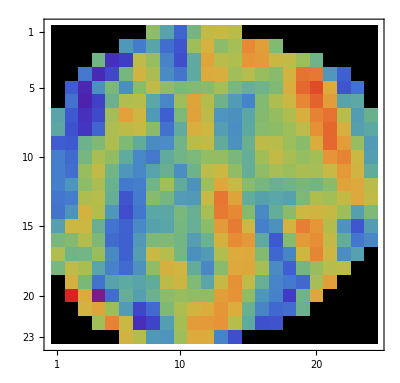
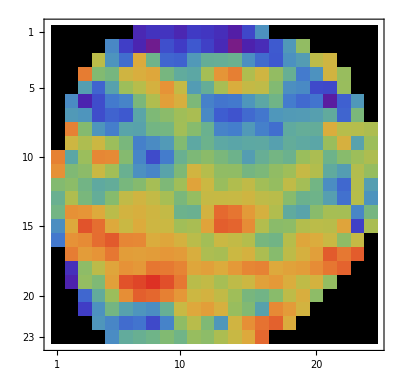
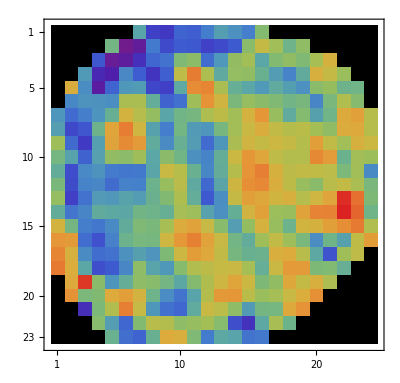
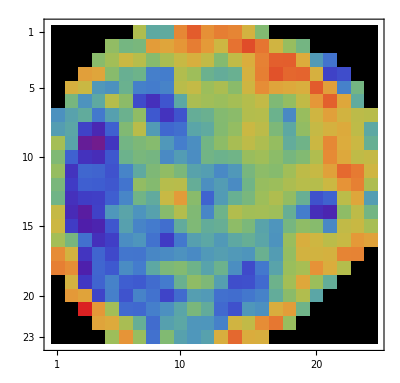
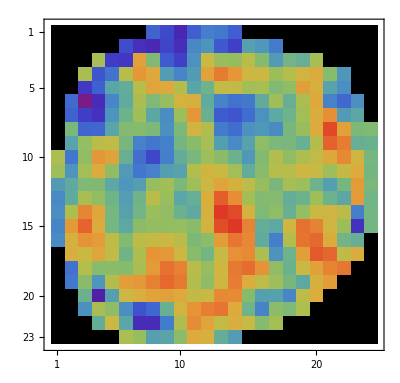
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,ColorFunction->"Rainbow",ColorRules->{0->Black}]&/@({DVxx,DVyy,DVyx,DVxy,DVww,trace}/.None-> 0)
```

```mathematica
Unprotect[None,Power];
None/:Subtract[None,None]:=None;
None/:Subtract[None,_Real|_Integer]:=None;
None/:Subtract[_Real|_Integer,None]:=None;
None/:Plus[None,-None]:=None;
None/:Plus[None,_Real|_Integer]:=None;
None/:Times[Rational[_,_],None]:=None;
None/:Times[_Integer|_Real,None]:=None;
None/:Times[None,None]:=None;
Power/:Times[_,Power[None,_]]:=None;
Protect[None,Power];
```

```mathematica
pos=SparseArray[(DVxx*DVyy*DVxy)/.None->0]["NonzeroPositions"];
```

```mathematica
graphicsPrimitive={};
Do[
DV={{(DVxx[[Sequence@@i]]-DVyy[[Sequence@@i]])/2,DVxy[[Sequence@@i]]},{DVxy[[Sequence@@i]],-(DVxx[[Sequence@@i]]-DVyy[[Sequence@@i]])/2 }};

If[FreeQ[DV,None],
{eVa,eVe}={DiagonalMatrix@#[[1]],#[[2]]ᵀ}&[Re@getEigensystem[DV]];
vp1=Diagonal[eVa];
{val1,ind1}={Sort@vp1,Ordering@vp1};
ϕ= ArcTan[eVe[[2,ind1[[2]] ]]/eVe[[1,ind1[[2]] ]] ];
rvect={eVe[[1,ind1[[2]] ]],eVe[[2,ind1[[2]] ]]};
speed=meanflow[[All,2]];
anglevelmean = 45 Degree;
rotationTrans=RotationTransform[anglevelmean];
rvectTurned=rotationTrans[rvect];
scalar=Abs[First@rvectTurned];
minDv = eVa[[1,1]]~Min~eVa[[2,2]];
maxDv = eVa[[1,1]]~Max~eVa[[2,2]];
{DphiDev,DmaxDev ,DminDev}= {ϕ,maxDv,minDv};
Tracee = (DVxx[[Sequence@@i]] + DVyy[[Sequence@@i]])/2;

Block[{prim},
If[Abs[DminDev]*Abs[DmaxDev] >0,
prim=GeometricTransformation[
Circle[array[[Sequence@@i]],{Round[1000Abs[Tracee]],0}],
RotationTransform[DphiDev,array[[Sequence@@i]]]
];

If[Tracee>0,
AppendTo[graphicsPrimitive,Prepend[{prim},XYZColor[0,0,1,0.33]]],
AppendTo[graphicsPrimitive,Prepend[{prim},XYZColor[1,0,0,0.33]]]
];

AppendTo[graphicsPrimitive,
{GrayLevel[0.1],GeometricTransformation[
Circle[array[[Sequence@@i]],{Round[360*DmaxDev],Round[Abs[360*DminDev]]}],
RotationTransform[DphiDev,array[[Sequence@@i]]]
]}]
]
],
DphiDev=DmaxDev=DminDev=None;
],{i,pos}];
```

```mathematica
{pt,dir}=Mean/@{N@meanflow[[All,1]],meanflow[[All,2]]};
midimage=Ceiling[Length[images]/2];
Image[ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[midimage]],Pi/2],
Graphics[If[FreeQ[#,0,Infinity],{Thick,#},{Thickness[0.006],#}]&/@graphicsPrimitive],
With[{reg=ConvexHullMesh@meanflow[[All,1]]},
ListVectorPlot[meanflow,VectorColorFunction->"Rainbow",VectorPoints->Fine,
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorScale->{0.075,0.30}]
],
Graphics[{GrayLevel[0.25],Thick,Arrowheads[{{.025,1,{-Graphics-,1}}}],Arrow[{pt,(pt+200dir)}]}],
ImageSize->Large],"Image",ImageResolution->500],-Pi/2],ImageSize->500]
```

-Graphics-

```mathematica
graphicsPrimitiveC=Replace[graphicsPrimitive,
HoldPattern[{t_,u_[Circle[v_,{w_Integer,0}],x_]}]:> {t,u[Circle[v,{w,1}],x]},{1}];
cases=Cases[graphicsPrimitiveC,Circle[_,{_,_}],{3}];
posprims=Position[Map[Length][Quiet@RandomPoint[#,100]&/@cases],x_/;x==100];
pickprims=Extract[graphicsPrimitiveC,posprims];
pickprimsOrig=Extract[graphicsPrimitive,posprims];
pickprimsOrig=Quiet@With[{reg=ConvexHullMesh@meanflow[[All,1]]},
Pick[pickprimsOrig,
(Or@@RegionMember[reg,RandomPoint[#,100]]&/@Cases[pickprims,Circle[_,{_,_}],{3}]),True]
];
Graphics@pickprimsOrig
```

-Graphics-

```mathematica
plt=Image[ImageRotate[
Rasterize[Show[
ImageRotate[ImageAdjust@images[[midimage]],Pi/2],
Graphics[If[FreeQ[#,0,Infinity],{Thick,#},{Thickness[0.006],#}]&/@pickprimsOrig],
With[{reg=ConvexHullMesh@meanflow[[All,1]]},
ListVectorPlot[meanflow,VectorColorFunction->"Rainbow",VectorPoints->Fine,
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorScale->{0.075,0.30}]
],
Graphics[{GrayLevel[0.25],Thick,Arrowheads[{{.025,1,{-Graphics-,1}}}],Arrow[{pt,(pt+200dir)}]}],
ImageSize->Large],"Image",ImageResolution->500],-Pi/2],
ImageSize->500]
```

-Graphics-

```mathematica
Rasterize[plt,"Image",ImageResolution->1000]
```